## Plot log((Z_(1-loop)(σ_0))/(Z_(1-loop)(∞)))

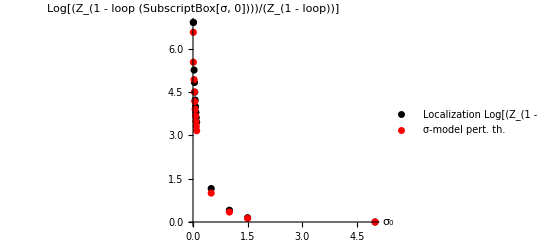

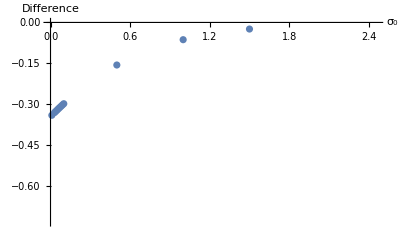

```mathematica
smpt=({{1/100, 6.56619506286976956351529783367654139599`5.817313780231524}, {2/200, 5.53154934890310629889952528808982939827`5.742846791239006}, {3/100, 4.92847666098710742599916342133262717387`5.69271270427518}, {4/100, 4.50212843630829910036748548933826802052`5.653417880354491}, {5/100, 4.17263784754486372380389979409399856117`5.620410692970024}, {6/100, 3.90443002635837652533284051864978176567`5.591557643981733}, {7/100, 3.67852819877839462202800379596470515163`5.565674089596111}, {8/100, 3.48360486426912096627892276656096149924`5.5420288882990265}, {9/100, 3.31235349373684785928929234254846400638`5.520136678410903}, {10/100, 3.15978518036761400333416367356306851409`5.499657557886685}, {50/100, 1.00126595009321127357483751254052333822`5.000549447426669}, {100/100, 0.34504399415518899183785895718076395565`4.537874472466664}, {150/100, 0.12518937176387857088670770353796446514`4.097567460022749}, {500/100, 0.00009025259429624538695796020936504005`0.9554596944818551}});
loc=Table[{σ0,-3/2 Log[Tanh[σ0]]},{σ0,smpt[[1;;Length[smpt],1]]}];

ListPlot[{loc,smpt},PlotStyle->{Black, Red},PlotLegends->{"Localization Log[(Z_(1 - loop (SubscriptBox[σ, 0])))/(Z_(1 - loop))]","σ-model pert. th."},
AxesLabel->{"σ_0","Log[(Z_(1 - loop (SubscriptBox[σ, 0])))/(Z_(1 - loop))]"},PlotRange->All]

ListPlot[{Table[{loc[[i]][[1]],smpt[[i]][[2]]-loc[[i]][[2]]},{i,1,Length[loc]}]},AxesLabel->{"σ_0","Difference"}]
```

σ_0     Δ Log[(Z_(1 - loop (SubscriptBox[σ, 0])))/(Z_(1 - loop))]     -1/2Log[1+ⅇ^(-2 σ0)]

(0.01 | -0.34161 | -0.341599
0.01 | -1.37626 | -0.341599
0.03 | -0.33181 | -0.331799
0.04 | -0.326985 | -0.326973
0.05 | -0.32221 | -0.322198
0.06 | -0.317485 | -0.317473
0.07 | -0.312809 | -0.312798
0.08 | -0.308183 | -0.308172
0.09 | -0.303607 | -0.303596
0.1 | -0.299081 | -0.299069
0.5 | -0.156639 | -0.156631
1. | -0.0634682 | -0.063464
1.5 | -0.0242954 | -0.0242937
5. | -0.0000459472 | -0.0000226994)

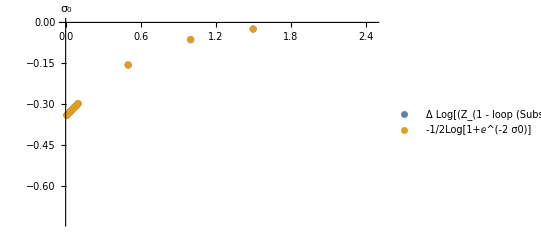

```mathematica
remainder=Table[{σ0,-1/2 Log[1+ⅇ^(-2σ0)]},{σ0,smpt[[1;;Length[smpt],1]]}];
Print["σ_0     Δ Log[(Z_(1 - loop (SubscriptBox[σ, 0])))/(Z_(1 - loop))]     -1/2Log[1+ⅇ^(-2 σ0)]"]
Table[{loc[[i]][[1]],smpt[[i]][[2]]-loc[[i]][[2]],remainder[[i]][[2]]},{i,1,Length[loc]}]//N//MatrixForm

ListPlot[{Table[{loc[[i]][[1]],smpt[[i]][[2]]-loc[[i]][[2]]},{i,1,Length[loc]}],Table[{loc[[i]][[1]],remainder[[i]][[2]]},{i,1,Length[loc]}]},AxesLabel->"σ_0",PlotLegends->{"Δ Log[(Z_(1 - loop (SubscriptBox[σ, 0])))/(Z_(1 - loop))]","-1/2Log[1+ⅇ^(-2 σ0)]"}]
```

## Plot d/dσ_0log((Z_(1-loop)(σ_0))/(Z_(1-loop)(∞)))

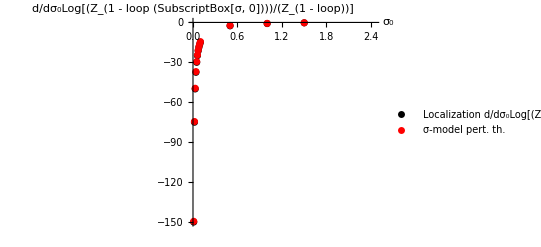

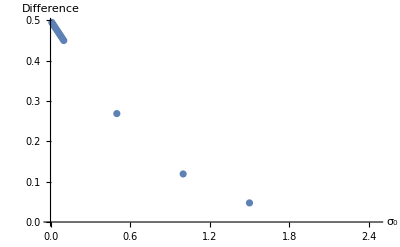

```mathematica
smpt=({{1/100, -149.49498098002266878600802831648633178188`7.174626612263991}, {2/100, -74.48999452592424501213062378474871082571`6.872097942359058}, {3/100, -49.48500249369434016616934278045975539613`6.694473596486398}, {4/100, -36.9800144911622726933977261951353522307`6.567967077007865}, {5/100, -29.47503327147122378499156529057761130588`6.469454303999805}, {6/100, -24.47006085653277991452565635669747846482`6.388635049434484}, {7/100, -20.89367053294207527868719713045164102556`6.320014742142668}, {8/100, -18.21014981633746116285298114243152963197`6.2603135187845425}, {9/100, -16.12188143190896252304237255411877445213`6.207415722817495}, {10/100, -14.45029570393172926405358005774448427961`6.159876734377815}, {50/100, -2.28381242056903056831340742489211551653`5.358660430547006}, {100/100, -0.70795865017529777392423546491732120563`4.85000789254129}, {150/100, -0.25203879582240596115568361186071195057`4.4014673959989}, {500/100, -0.0002270016750393484398198983002288461`1.3560290618524273}});
loc=Table[{σ0,-3 Csch[2 σ0]},{σ0,smpt[[1;;Length[smpt],1]]}];

ListPlot[{loc,smpt},PlotStyle->{Black, Red},PlotLegends->{"Localization d/dσ_0Log[(Z_(1 - loop (SubscriptBox[σ, 0])))/(Z_(1 - loop))]","σ-model pert. th."},
AxesLabel->{"σ_0","d/dσ_0Log[(Z_(1 - loop (SubscriptBox[σ, 0])))/(Z_(1 - loop))]"}]

ListPlot[{Table[{loc[[i]][[1]],smpt[[i]][[2]]-loc[[i]][[2]]},{i,1,Length[loc]}]},AxesLabel->{"σ_0","Difference"}]
```

σ_0     Δ d/dσ_0Log[(Z_(1 - loop (SubscriptBox[σ, 0])))/(Z_(1 - loop))]     1/(1 + SuperscriptBox[ⅇ, 2 σ0])

(0.01 | 0.495019 | 0.495
0.02 | 0.490009 | 0.490001
0.03 | 0.48501 | 0.485004
0.04 | 0.480015 | 0.480011
0.05 | 0.475025 | 0.475021
0.06 | 0.47004 | 0.470036
0.07 | 0.465061 | 0.465057
0.08 | 0.460088 | 0.460085
0.09 | 0.455124 | 0.455121
0.1 | 0.450169 | 0.450166
0.5 | 0.268942 | 0.268941
1. | 0.119203 | 0.119203
1.5 | 0.0474259 | 0.0474259
5. | 0.0000453979 | 0.0000453979)

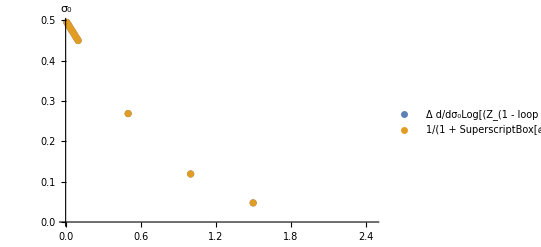

```mathematica
remainder=Table[{σ0,1/(1+ⅇ^(2 σ0))},{σ0,smpt[[1;;Length[smpt],1]]}];
Print["σ_0     Δ d/dσ_0Log[(Z_(1 - loop (SubscriptBox[σ, 0])))/(Z_(1 - loop))]     1/(1 + SuperscriptBox[ⅇ, 2 σ0])"]
Table[{loc[[i]][[1]],smpt[[i]][[2]]-loc[[i]][[2]],remainder[[i]][[2]]},{i,1,Length[loc]}]//N//MatrixForm

ListPlot[{Table[{loc[[i]][[1]],smpt[[i]][[2]]-loc[[i]][[2]]},{i,1,Length[loc]}],Table[{loc[[i]][[1]],remainder[[i]][[2]]},{i,1,Length[loc]}]},AxesLabel->"σ_0",PlotLegends->{"Δ d/dσ_0Log[(Z_(1 - loop (SubscriptBox[σ, 0])))/(Z_(1 - loop))]","1/(1 + SuperscriptBox[ⅇ, 2 σ0])"}]
```

## [Plot 1 in paper]

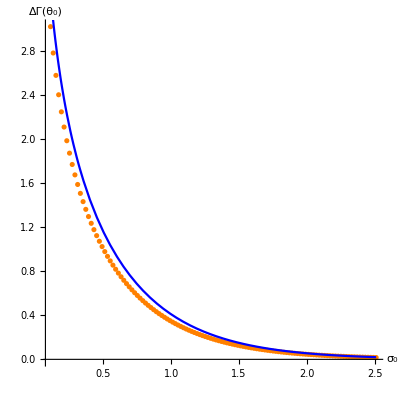

```mathematica
σ0init=11/100;
σ0fin=251/100;
σ0step=5/100;

grid={Table[i,{i,0,σ0fin,50/100}],Table[i,{i,0,-3/2 Log[Tanh[σ0init]],25/100}]};

smpt=ListPlot[Table[{σ0,N[-3/2 Log[Tanh[σ0]]-1/2 Log[1+ⅇ^(-2σ0)],{∞,5}]},{σ0,σ0init,σ0fin,2/100}],PlotRange->Full,AspectRatio->1,PlotStyle->Orange,AxesLabel->{Style["σ_0",FontFamily->"Arial",FontSize->18,TextAlignment->Left,LineBreakWithin->False],Style["ΔΓ(θ_0)",FontFamily->"Arial",FontSize->18,TextAlignment->Left,LineBreakWithin->False]},AxesStyle->16];

loc=Plot[-3/2 Log[Tanh[σ0]],{σ0,σ0init,σ0fin},PlotRange->Full,AspectRatio->1,PlotStyle->Blue,AxesStyle->16];

Show[smpt,loc,PlotLegends->{"ciao"}]
(*Table[ArcTanh[Cos[θ0]],{θ0,1 π/180,89 π/180,2 π/180}]
```

```mathematica
ClearAll[simpleLegend]
simpleLegend[legendItems__,pos_]:=Module[{legendLine,offset,legend},offset=Module[{s,o,insetpts=0},s=pos/.{Left->0,Right->1,Bottom->0,Top->1};
o=insetpts pos/.{Left->1,Right->-1,Bottom->1,Top->-1};
Offset[o,Scaled[s]]];
legendLine[{lbl_,lineStyle_}]:={Graphics[{lineStyle,Line[{{0,0.5},{1,0.5}}]},ImageSize->{70,50},AspectRatio->0.5],Style[lbl,FontFamily->"Arial",FontSize->18,TextAlignment->Left,LineBreakWithin->False]};
legend=GraphicsGrid[legendLine/@legendItems,Alignment->Left];
Graphics@Inset[legend,offset,pos]];

Show[smpt,loc,simpleLegend[Thread@{{"ΔΓ(θ_0)_loc","ΔΓ(θ_0)_sm"},{Directive[Blue,Thick],Directive[Orange,Dotted,Thick]}},{Right,Top}]]
```

-Graphics-

## [Plot 2 in paper]

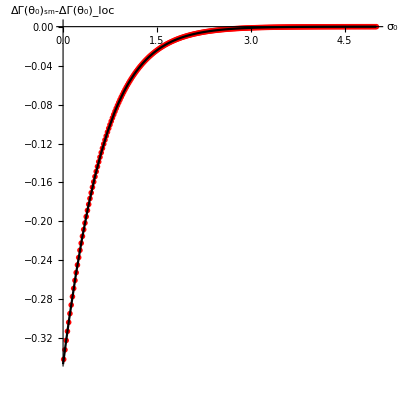

```mathematica
σ0init=1/100;
σ0fin=501/100;
σ0step=5/100;

grid={Table[i,{i,0,σ0fin,50/100}],Table[i,{i,-40/100,0,5/100}]};

smpt=ListPlot[Table[{σ0,-1/2 Log[1+ⅇ^(-2σ0)]},{σ0,σ0init,σ0fin,2/100}],PlotRange->Full,AspectRatio->1,PlotStyle->
{Red,PointSize[0.01]},AxesLabel->{"σ_0","ΔΓ(θ_0)_sm-ΔΓ(θ_0)_loc"},PlotRange->{{0/100,501/100},{-1/2 Log[1+ⅇ^(-2σ0init)],0}},AxesStyle->16];

loc=Plot[N[-1/2 Log[1+ⅇ^(-2σ0)],{∞,5}],{σ0,0,σ0fin},PlotRange->Full,AspectRatio->1,PlotStyle->{Black,Thickness[0.004]},PlotRange->{{0/100,501/100},{-1/2 Log[1+ⅇ^(-2σ0init)],0}},AxesStyle->16];

Show[smpt,loc]
(*Table[ArcTanh[Cos[θ0]],{θ0,1 π/180,89 π/180,2 π/180}]
```